# Rania – 02.4.2025 EIWL3 Section 14-17

Section 14 Problems

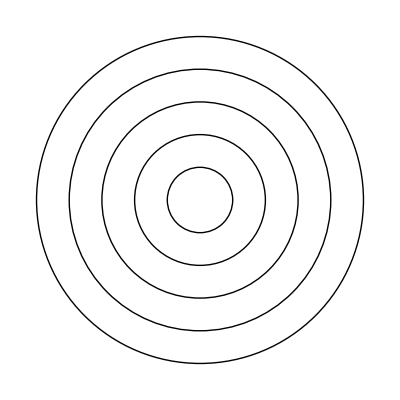

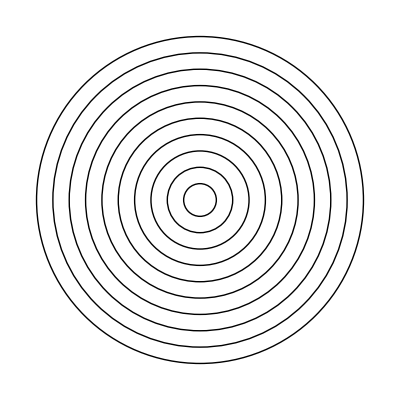

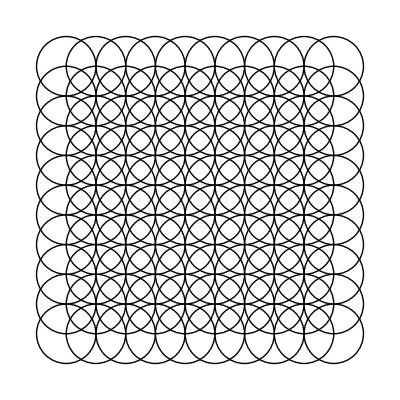

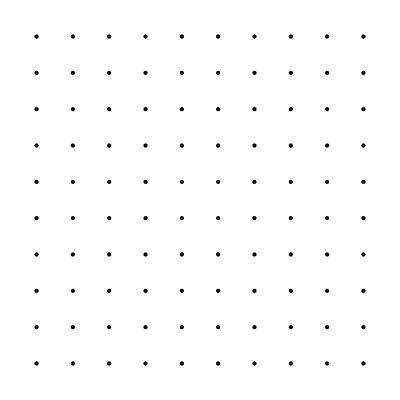

-Graphics3D-

-Graphics3D-

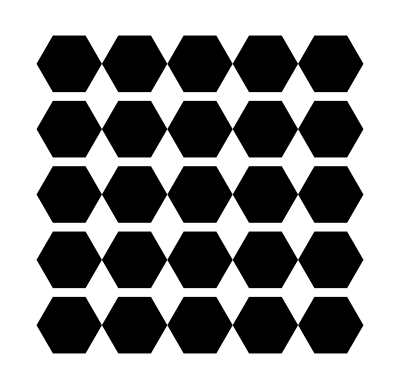

-Graphics3D-

```mathematica
(*14.1 5 concentric circles centered at {0,0} with radii 1,2,...,5. *)
Graphics[Table[Circle[{0,0}, r], {r,5}]]
(*14.2 10 concentric circles with random colors*)
Graphics[Table[Style[Circle[{0,0},r], RandomColor[]],{r,10}]]
(*14.3 Graphics of a 10×10 grid of circles with radius 1 centered at integer points {x,y}*)
Graphics[Table[Circle[{x,y},1],{x,10}, {y,10}]]
(*14.4 A 10×10 grid of points with coordinates at integer positions up to 10*)
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
(*14.5 A Manipulate with between 1 and 20 concentric circles*)
Manipulate[Graphics[Table[Circle[{0,0}, r],{r,1,n}]],{n,20,1}]
(*14.6 Place 50 spheres with random colors at random integer coordinates up to 10*)
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],RandomColor[]],50]]
(*14.7 An 11×11×11 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at integer coordinates,and should just touch each other*)
Graphics3D[Table[{RGBColor[x/10,y/10,z/10],Sphere[{x,y,z},1/2]},{x,11},{y,11},{z,11},{h,0,1.1,.1}]]
(*Doing it to 1/2 makes the sphere barely touch, but I'm not sure why....*)
(*14.8 A Manipulate with t varying between−2 and+2 that contains circles of radius x centered at {t*x,0} with x going from 1 to 10*)
Manipulate[ Graphics[Table[Circle[{t*x,0},x],{x,1,10}]],{t,-2,2}]
(*14.9 A 5×5 array of regular hexagons with size 1/2,centered at integer points*)
Graphics[Table[RegularPolygon[{x,y},1/2,6],{x,5},{y,5}]]
(*14.10 A line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50*)
Graphics3D[Line[Table[RandomInteger[50,3],50]]]
(*14.11 Manipulate of an icosahedron with side length varying from 1 to 2 and a dodecahedron with side length 1,both having opacity 0.5 and the same center *)
Manipulate[Graphics3D[{Style[Dodecahedron[{1,1,1},1],Opacity[.5]], Style[Icosahedron[{1,1,1},n],Opacity[.5]]}],{n,1,2,.1}]
```

Section 17 Problems

2.04117 kg

96.963 km/h

0.205052 mi

26.8147

81.3

16.17 $

305.353 kg

{0.0000726776 ly,0.000165148 ly,0.000306766 ly,0.000484163 ly,0. ly}

hello

{A,A,A,A,A,A,A,A,A,A,A,A,A}

-Graphics-

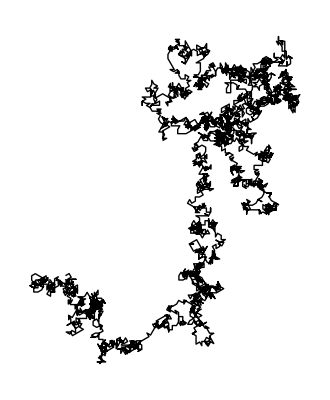

-Graphics-

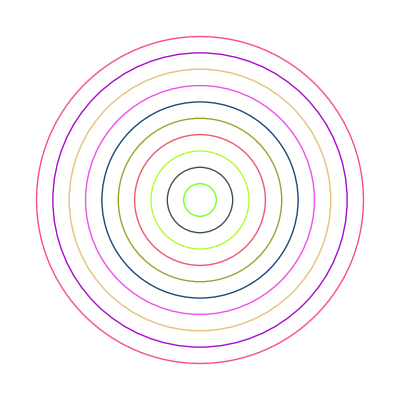

-Graphics-

-Graphics-

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics3D-

```mathematica
(*17.1 4.5 lbs (pounds) to kilograms*)
UnitConvert[Quantity[4.5, "Pounds"],"kilograms"]
(*17.2 60.25 mph to kilometers per hour*)
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],Quantity[, ("Kilometers")/("Hours")] ]
(*17.3 The height of the Eiffel Tower in miles*)
UnitConvert[Entity["Building","EiffelTower::5h9w8"]["Height"],"Miles"]
(*17.4 The height of Mount Everest divided by the height of the Eiffel Tower *)
(Entity["Mountain","MountEverest"]["Elevation"])/(Entity["Building","EiffelTower::5h9w8"]["Height"])
(*17.5 The mass of the Earth divided by the mass of the Moon*)
(Entity["Planet","Earth"]["Mass"])/(Entity["PlanetaryMoon","Moon"]["Mass"])
(*17.6 2500 Japanese yen to US dollars*)
CurrencyConvert[Quantity[2500., "Yen"],Quantity[, "USDollars"]]
(*17.7 The total of 35 ounces,1/4 ton,45 lbs and 9 stone in kilograms*)
UnitConvert[Quantity[35, "Ounces"]+Quantity[0.25, "ShortTons"]+Quantity[45, "Pounds"]+ Quantity[9, "Stones"], "Kilograms" ]
(*17.8 Planets distance in light years*)
UnitConvert[EntityClass["Planet",{EntityProperty["Planet","Radius"]->TakeLargest[5]}][EntityProperty["Planet","DistanceFromEarth"]], "LightYears"]
(*17.9 Rotate the string "hello" by 180 degrees*)
Rotate["hello",180 °]
(*17.10 A table of a size-100 “A” rotated by 0° through 360° in steps of 30°*)
Table[Style[Rotate["A",x Quantity[, "AngularDegrees"]],100],{x,0,360,30}]
(*17.11 Manipulate to rotate an image of a cat between 0° and 180°*)
Manipulate[Rotate[["Image"],x Quantity[, "AngularDegrees"]],{x,0,180,10}]
(*17.12 Generate graphics for a path obtained by turning 0°,1°,2°,...,180°*)
Graphics[Line[AnglePath[Table[n Quantity[, "AngularDegrees"], {n,0,180, 1}]]]]
(*17.13 Graphics of the path obtained by turning a constant angle 100 times,controlling the angle from 0° to 360° with a Manipulate*)
Manipulate[Graphics[Line[AnglePath[Table[n Degree,100]]]],{n,0,360}]
(*17.14 Graphics of the path obtained by successively turning by the digits of 2^10000 multiplied by 30 degrees *)
Graphics[Line[AnglePath[IntegerDigits[2^10000]*30 Degree]]]
```